```mathematica
elementList={"Sc"->1,"Ti"->2,"V"->3,"Cr"->4,"Mn"->5,"Fe"->6,"Co"->7,"Ni"->8,"Cu"->9,"Zn"->10,"Y"->11,"Zr"->12,"Nb"->13,"Mo"->14,"Tc"->15,"Ru"->16,"Rh"->17,"Pd"->18,"Ag"->19,"Hf"->20,"Ta"->21,"W"->22,"Re"->23,"Os"->24,"Ir"->25,"Pt"->26,"Au"->27};
elements=List@@@elementList//Transpose//First;
```

## Parse Data:

```mathematica
data=Import["/home/marco/fridbDemo/allresults.json"];
atoms32=Select[data,StringCases[#[[1]],"32"]≠{}&];
atoms32Binding=Select[atoms32,StringCases[#[[1]],"Binding"]≠{}&];
dataall={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms32Binding)/.elementList;
tab=Table[Cases[dataall,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
smallBindingTable = Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;


atoms79=Select[data,StringCases[#[[1]],"60"]≠{}&];
atoms79Binding=Select[atoms79,StringCases[#[[1]],"Binding"]≠{}&];
dataall79={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79Binding)/.elementList;
tab=Table[Cases[dataall79,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
bigBindingTable = Table[With[{x=Cases[dataall79,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

## Make Matrix Plots:

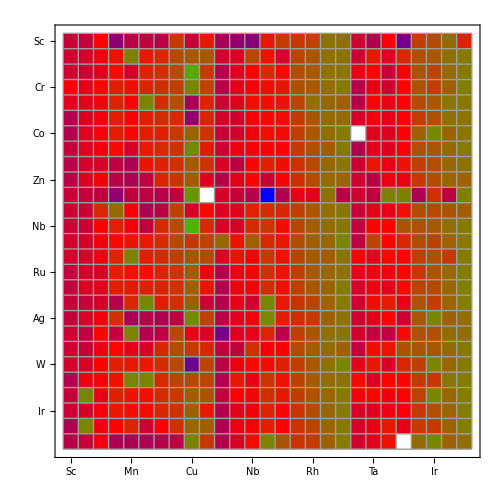

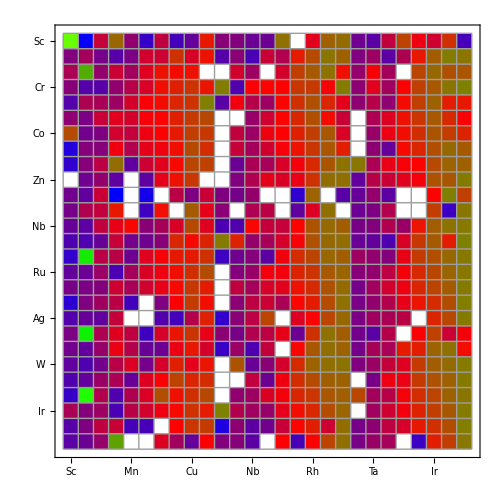

{target→-1.51,r1→0.5}

MatrixPlot::crule: Value of option ColorRules -> {0 → GrayLevel[1], #1 < target + r1 && #1 > target - r1 &, _ → RGBColor[1, 1, 0]} is not a valid list of color rules.

MatrixPlot[{{156.593,-52.0823,-4.8808,-1.38635,-5.99529,-20.0851,-5.10796,-13.6342,-7.31414,-3.21067,-6.26199,-6.32499,-6.99733,-6.96793,-1.04173,0,-4.19145,-1.51104,-1.16187,-6.84807,-8.31656,-5.06085,-2.33724,-4.02743,-4.54608,-2.71657,-13.4038},{-6.37856,-5.59122,-6.65324,-8.56062,-6.5031,-4.48815,-4.66779,-2.6822,-4.34957,-3.26492,-9.05846,-6.16257,-11.9453,-4.83061,-5.39006,-3.14056,-2.13722,-0.944052,-1.48643,-6.40109,-5.74353,-8.04924,-5.42099,-3.22566,-1.65532,-0.458595,-0.939026},{-5.44699,30.0255,-5.91967,-4.72777,-5.62339,-4.27073,-3.27165,-3.40732,-3.28215,0,0,-4.46658,-5.73677,0,-4.45973,-2.40427,-1.69657,-0.984736,-3.31205,-5.87579,-3.86687,-5.60527,0,-2.27232,-1.3077,-2.03932,-1.80741},{-6.2748,-9.00658,-8.85705,-6.01922,-5.2545,-4.37119,-3.33897,-3.0514,-2.61911,-3.25315,-0.396658,-10.1905,-3.72415,-3.64999,-3.66131,-2.59028,-2.54304,-3.79014,-0.541609,-6.07267,-4.23228,-5.66255,-3.66237,-2.34703,-1.69778,-0.868226,0.094805},{-9.55682,-5.45035,-5.55298,-5.74034,-4.45107,-3.74383,-3.39876,-3.00489,-2.63506,-0.059809,-8.48092,-3.92556,-5.29579,-5.72172,-3.53883,-2.73634,-2.03151,-2.97777,-4.18021,-6.07235,-5.28069,-6.0437,-3.40745,-2.44283,-1.47908,-3.12281,-3.20889},{-6.03791,-6.49868,-4.77141,-4.22212,-4.44748,-3.83976,-3.606,-3.07364,-2.50812,-2.23149,0,0,-5.81723,-4.59753,-3.59163,-2.90435,-2.07263,-3.38265,-4.79914,0,-5.44393,-4.29912,-3.27759,-2.60705,-1.67576,-2.82553,-3.74054},{-2.13313,-6.73442,-6.44987,-4.51661,-5.0027,-4.0214,-3.69181,-3.18625,-2.43546,-2.55563,0,-5.0967,-5.752,-4.01782,-3.6628,-3.04472,-2.38072,-1.73579,-4.3378,0,-5.81695,-4.07637,-3.36863,-2.77778,-1.84671,-2.48347,-3.0152},{-31.5438,-6.30326,-6.28642,-3.95795,-5.35709,-4.17482,-3.92596,-3.32734,-2.1846,-2.76281,0,-4.8582,-5.58102,-4.54124,-3.86836,-3.2556,-2.57638,-1.78563,-3.10561,0,-6.0922,-7.19354,-3.4598,-2.99067,-2.05009,-1.28481,-1.67519},{-22.6138,-6.28988,-5.16385,-1.15129,-7.63872,-4.68688,-4.21042,-3.47031,-2.31971,-2.33926,0,-7.01125,-5.54141,-5.5682,-4.41937,-3.8825,-2.87675,-1.84559,-0.968065,-0.857359,-5.45429,-4.10056,-3.82665,-3.55258,-2.16113,-1.4355,-1.48154},{0,-6.85377,-5.87728,-7.85179,0,-7.85115,-4.1657,-3.27465,-2.56685,0,0,-6.33526,-5.3924,-4.17302,-4.34855,-4.09424,-2.64932,-1.16132,-1.1105,-7.43567,-5.236,-4.78228,-4.2183,-3.88105,-1.9626,-1.72539,-0.651161},{-6.82508,-7.6647,-4.75368,-55.2225,0,-41.2744,0,-5.19292,-6.45196,-4.80069,-6.43553,-6.58901,-5.95398,0,0,-24.5528,-1.43653,0,-8.40646,-7.19498,-5.89726,-8.00436,0,0,-3.53585,0.081853,-2.36321},{-6.54231,-5.41495,-5.01433,-3.20714,0,-16.4333,-3.3022,0,-1.66518,-4.16464,-6.12528,0,-5.44282,-5.16067,0,-7.71559,-4.33076,-1.0618,0,-6.9115,-6.45084,-5.31988,0,0,-2.46452,-18.5892,-0.852168},{-7.23153,-7.86752,-5.06282,-4.13799,-3.47719,-6.19052,-5.55679,-4.40342,-2.19829,-4.27462,-10.7726,-10.2808,-3.47951,-4.98922,-4.91814,-3.52981,-1.89493,-1.25212,-1.61386,-6.51928,-6.31761,-5.38088,-5.79215,-3.25711,-1.64426,-0.959019,-0.720287},{-10.756,-10.5417,-7.15487,-4.89839,-6.73034,-6.8468,-6.2396,-2.98639,-3.4746,-3.01487,-0.641215,-3.03758,-5.84587,-5.55302,-4.4492,-3.82204,-2.01964,-1.27028,-1.12215,-7.10821,-7.49273,-10.6245,-4.367,-2.55391,-1.6666,-3.14932,0.111381},{-22.603,72.4589,-5.22013,-5.24007,-6.88519,-4.24537,-3.78087,-3.20044,-3.16981,-2.736,-17.1324,-6.85328,-6.31002,-7.91438,-3.93627,-2.78939,-2.32384,-1.34162,-1.55604,-5.71086,-5.98986,-6.31628,-4.08815,-2.48876,-2.08589,-1.30003,-0.779364},{-7.46873,-7.01377,-5.76516,-11.4913,-5.57855,-4.35254,-3.99095,-3.31243,-2.75112,-2.12852,0,-6.29196,-5.80493,-3.89637,-3.89554,-3.03023,-2.61636,-1.71012,-1.40126,-6.26991,-5.95577,-5.1579,-3.89365,-2.80904,-2.27338,-1.41603,-0.841554},{-6.53148,-6.46886,-6.32256,-4.60922,-5.54535,-4.5057,-4.12425,-3.46507,-2.57443,-3.12491,0,-5.12742,-5.57374,-4.40407,-4.19734,-3.27703,-2.80686,-1.9561,-1.23439,-6.56118,-5.64565,-4.47094,-3.99962,-2.99608,-2.32101,-1.65717,-0.643193},{-26.4238,-6.42489,-5.7072,-5.20112,-15.3684,0,-6.4174,-3.74573,-2.49978,-3.35264,0,-6.10207,-5.14771,-4.70325,-5.51858,-3.52497,-3.13165,-2.1422,-1.01761,-6.50597,-5.95755,-5.32005,-4.14755,-3.25501,-2.79004,-2.08796,-0.219267},{-9.48667,-7.22416,-7.61397,-4.97316,0,0,-10.1278,-14.0154,-5.3164,-3.03813,-22.1191,-6.18933,-5.15968,-2.3297,0,-4.30826,-3.59356,-2.27424,-1.31265,-6.49365,-5.70296,-5.53729,-5.18588,0,-3.00177,-2.26764,-0.687724},{-6.49527,77.4955,-5.43846,-4.26979,-5.10641,-16.4765,-4.42716,-3.25269,-2.6162,-4.13958,-6.10936,-6.51492,-5.35746,-5.14636,-4.15613,-6.95254,-2.68467,-0.996253,-1.63032,-6.74177,-8.17665,-5.30903,0,-3.7366,-2.33952,-4.72443,-3.88743},{-6.73456,-7.62512,-5.82792,-4.05768,-5.30823,-7.1874,-6.94179,-4.07301,-3.243,-4.44244,-19.4731,-5.7818,-10.7687,-5.02971,0,-3.49095,-1.72916,-1.078,-1.4456,-6.65057,-5.5707,-5.50631,-3.14936,-3.10261,-1.4505,-1.01418,-3.35841},{-7.75414,-10.7218,-6.74184,-5.23555,-4.31584,-6.55669,-4.44321,-3.08222,-4.15872,-3.25324,0,-1.96167,-7.14468,-6.17939,-4.46033,-2.79696,-1.42328,-1.09775,-0.944587,-6.40989,-5.74936,-4.96581,-4.25726,-2.50761,-1.61137,-1.165,-0.567407},{-10.3359,-7.44983,-5.78559,-5.47188,-7.16346,-4.2842,-3.74287,-2.3344,-3.00927,-2.7963,0,0,-5.07971,-6.90573,-3.95543,-2.77372,-2.1205,-1.55419,-1.45256,0,-6.51167,-4.04436,-4.07529,-2.5065,-1.98747,-1.49275,-0.674697},{-21.2592,105.779,-5.32714,-10.4653,-5.40727,-4.31596,-2.08305,-3.2792,-2.7509,-2.20954,0,-5.97963,-5.7127,-4.34306,-3.88377,-2.94576,-2.60827,-1.81742,-1.49496,-2.26365,-5.60984,-5.25255,-3.87176,-2.78006,-2.33175,-1.47851,-0.910055},{-5.51665,-6.31019,-5.71959,-11.8951,-5.24787,-4.4703,-4.04416,-3.41553,-2.68085,-3.15356,0.261878,-5.32218,-5.6989,-5.82154,-4.17536,-3.32817,-2.84217,-2.12423,-1.38007,0,-5.68724,-4.54729,-3.90102,-3.02631,-2.4071,-1.7472,-0.631855},{-8.9796,-6.43582,-5.1351,-4.84425,-13.2155,-12.8477,0,-3.59671,-2.60771,-2.50213,-35.5089,-6.05737,-7.88889,-6.82775,-4.85534,-3.49378,-3.05986,-4.61632,-1.12108,-6.53823,-6.08206,-5.1222,-4.43949,-3.18952,-2.74291,-2.09483,-0.14646},{-8.11528,-6.96224,-5.8536,21.348,0,0,-4.2824,-5.63446,-7.42065,-3.7113,-6.39691,-6.24734,-8.14896,0,-3.73138,-13.0327,-3.65912,-2.32996,-1.04517,-6.53468,-5.79186,-5.57802,0,-17.8416,-3.11806,-2.45439,-0.786697}},ColorRules→{0→GrayLevel[1],#1<target+r1&&#1>target-r1&,_→RGBColor[1,1,0]},Mesh→True,Frame→True,FrameTicks→{{{1,Sc},{2,Ti},{3,V},{4,Cr},{5,Mn},{6,Fe},{7,Co},{8,Ni},{9,Cu},{10,Zn},{11,Y},{12,Zr},{13,Nb},{14,Mo},{15,Tc},{16,Ru},{17,Rh},{18,Pd},{19,Ag},{20,Hf},{21,Ta},{22,W},{23,Re},{24,Os},{25,Ir},{26,Pt},{27,Au}},{{1,Sc},{2,Ti},{3,V},{4,Cr},{5,Mn},{6,Fe},{7,Co},{8,Ni},{9,Cu},{10,Zn},{11,Y},{12,Zr},{13,Nb},{14,Mo},{15,Tc},{16,Ru},{17,Rh},{18,Pd},{19,Ag},{20,Hf},{21,Ta},{22,W},{23,Re},{24,Os},{25,Ir},{26,Pt},{27,Au}}},PlotRangePadding→None,ImageSize→500]

```mathematica
MatrixPlot[smallBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

subs = {target -> -1.51, r1 -> 0.5}
MatrixPlot[bigBindingTable,ColorRules->{0->White, #<(target + r1)&& #> (target-r1) & /. subs -> Green, _ -> Yellow },Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]
```

## Make Bar Charts:

### These statements are used to filter out spurious binding energies. Then nanoparticle removed has its corresponding label removed, so that the bar chart bars and their labes line up correctly

{{12}}

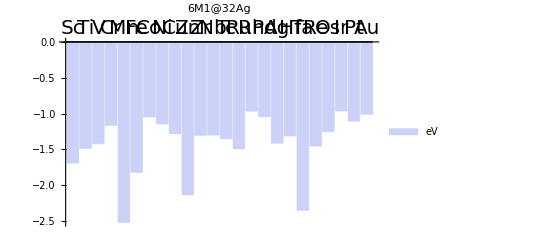

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

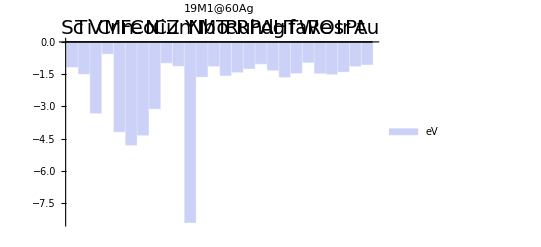

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

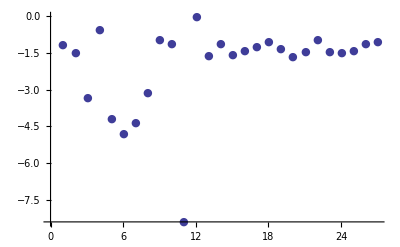

-Graphics-

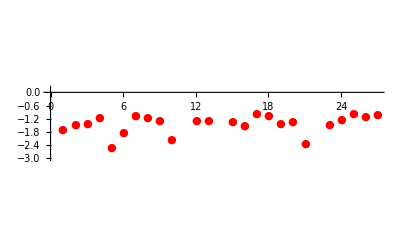

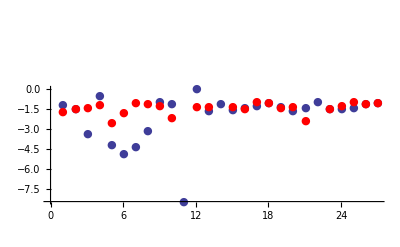

{0.528839,0.00008181,-1.8915,0.6229,-1.66226,-2.97975,-3.29121,-1.96083,0.313333,1.02347,1.6646,1.30394,-0.314616,-5.48928,-0.205317,0.0908144,-0.267932,0.0252885,0.100085,-0.317968,0.904503,-5.36616,0.00134848,-0.242626,-0.417037,-0.0155537,-0.0349103}

```mathematica
placeholder =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
removedElementsPos = Position[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
newElementsSmall = Delete[elements, # & /@removedElementsPos] ;

placeholder2 =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,bigBindingTable[[All,19]] ],0];
removedElementsPos2 = Position[Map[ If[# >0 || # <-10,0,#] &,bigBindingTable[[All,19]] ],0]
newElementsBig = Delete[elements, # & /@removedElementsPos2] ;
newElementsSmall == newElementsBig;
Delete[placeholder2, 1] ;

BarChart[placeholder,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsSmall,Above]},PlotLabel->Style["6M1@32Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements

BarChart[placeholder2,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsBig,Above]},PlotLabel->Style["19M1@60Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements
p1 = ListPlot[{#} & @bigBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}]


Show[p1,Graphics[{Red,elements}] ]
p2 = ListPlot[smallBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}, PlotStyle -> Red]
Show[p1,p2]
bigBindingTable[[All, 19]] - smallBindingTable[[All,19]]
```

{-0.908268,1.17983,-0.161612,1.42834,-1.82744,-1.27757,-0.246482,0.721737,0.642848,0.356941,8.06999,-15.6221,0.820824,-0.974981,2.18515,0.620228,0.418727,0.0693048,-0.0156052,-3.08539,0.793764,0.845849,-0.263005,0.585449,0.352614,0.156198,-0.137576}

-1.51

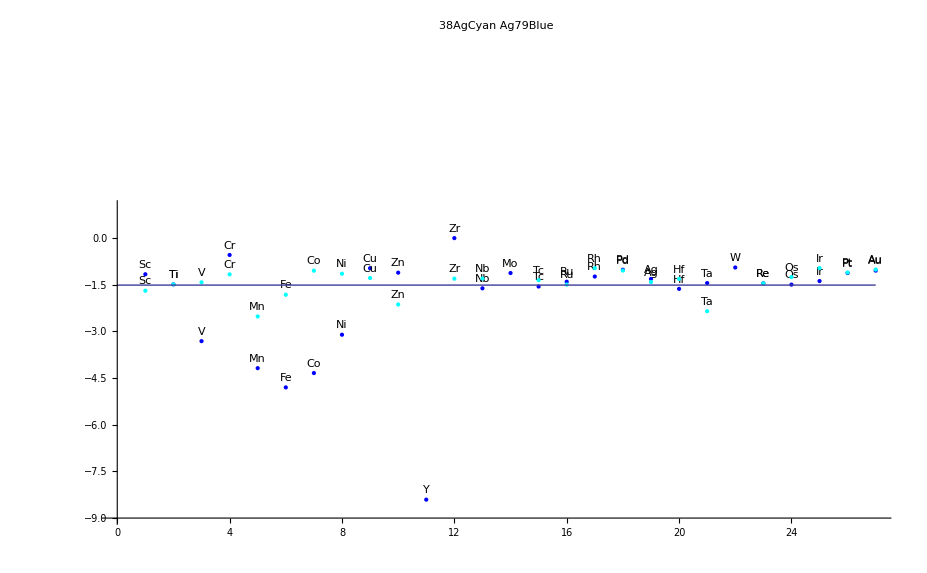

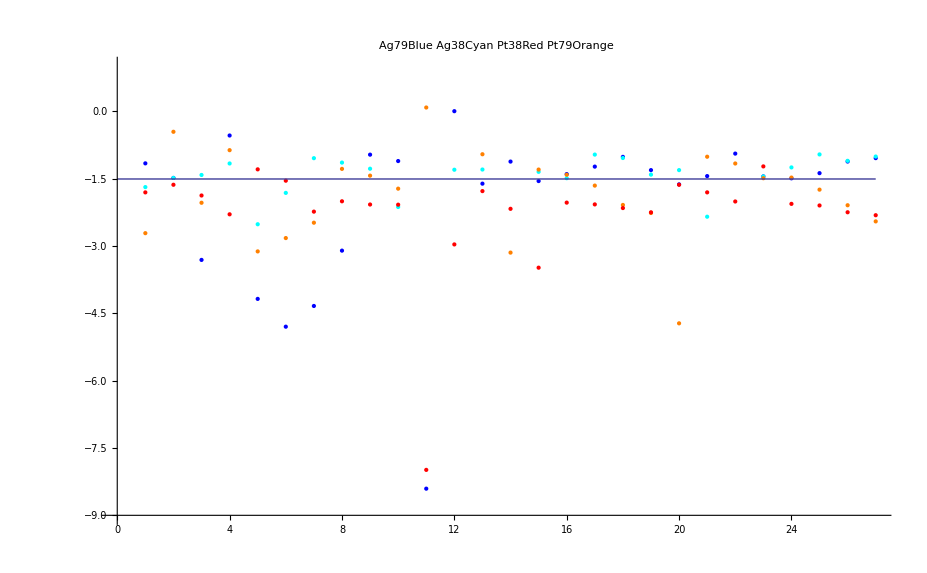

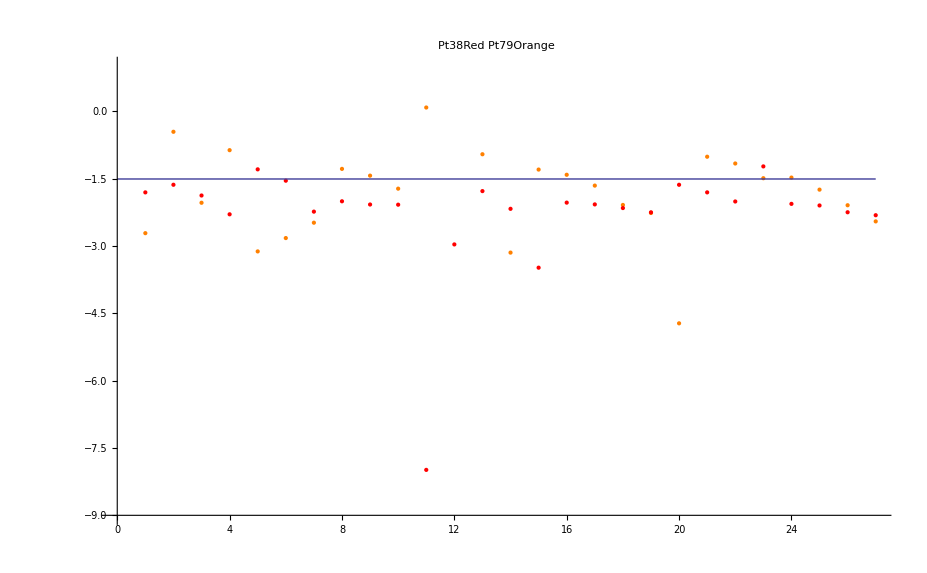

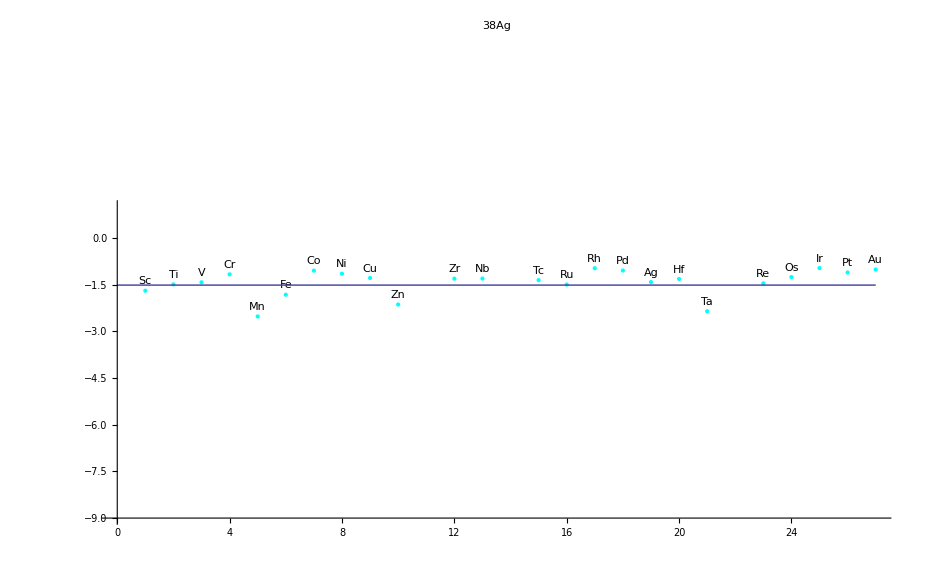

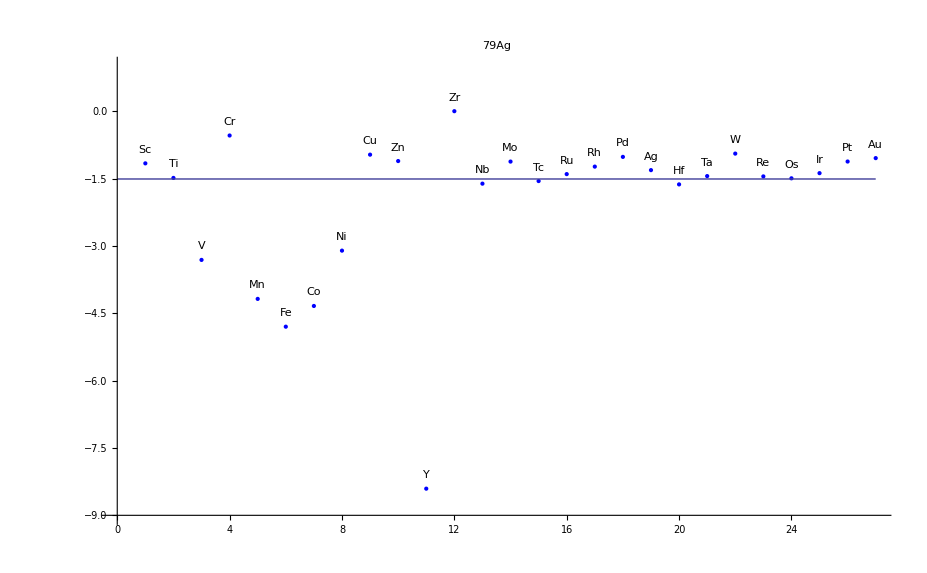

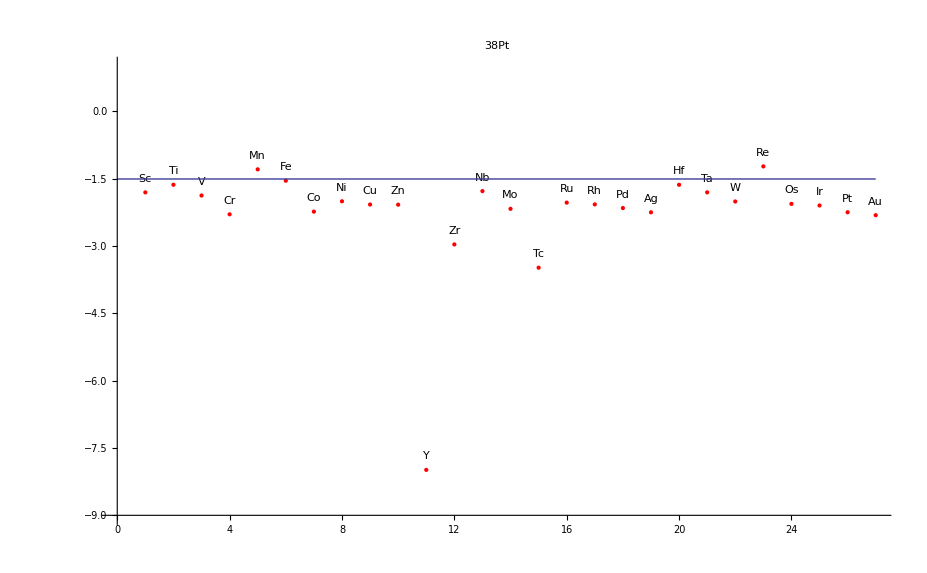

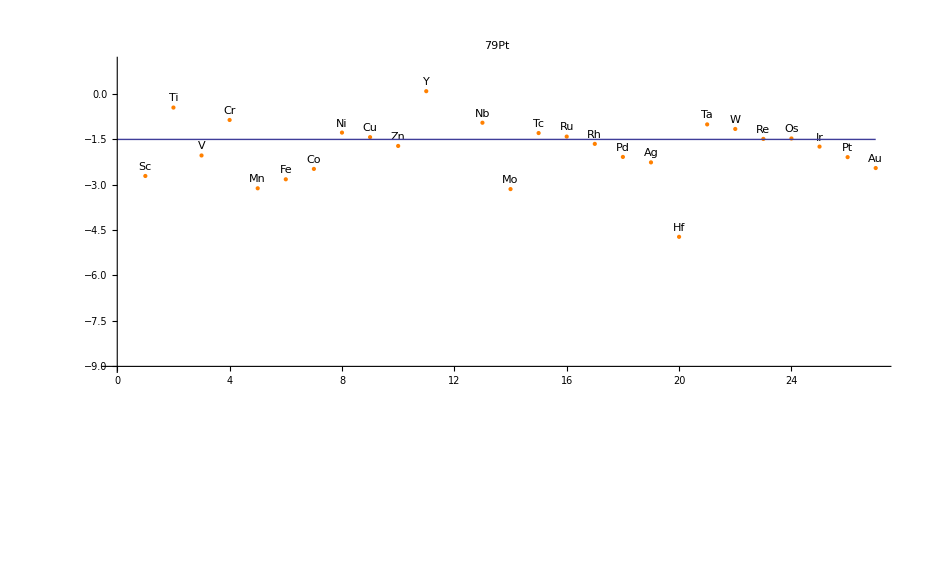

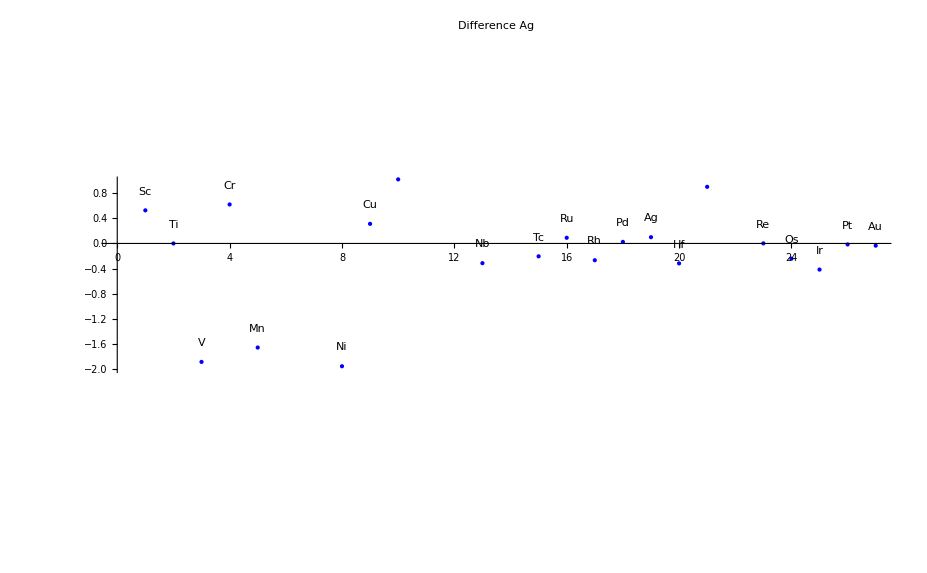

```mathematica
dataPlot1=ListPlot[smallBindingTable[[All,19]],PlotStyle->{Cyan, PointSize->Large},AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}, PlotLabel->"38Ag",  PlotLegends->Automatic];
labels1=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@smallBindingTable[[All,19]]],smallBindingTable[[All,19]]}];


dataPlot2=ListPlot[bigBindingTable[[All,19]],PlotStyle->{Blue,PointSize->Large},AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}, PlotLabel -> "79Ag",  PlotLegends->Automatic];
labels2=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@bigBindingTable[[All,19]]],bigBindingTable[[All,19]]}];

differenceAg = bigBindingTable[[All,19]] - smallBindingTable[[All, 19]];

diffAgPlot=ListPlot[differenceAg,PlotStyle->{Blue,PointSize->Large},AxesOrigin->{0,0},PlotRange->{Automatic,{-2,1}}, PlotLabel -> "Difference Ag",  PlotLegends->Automatic];
diffAgLabel=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@differenceAg],differenceAg}];





dataPlot3=ListPlot[smallBindingTable[[All,26]],PlotStyle->{Red, PointSize->Large},AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}, PlotLabel -> "38Pt"];
labels3=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@smallBindingTable[[All,26]]],smallBindingTable[[All,26]]}];

dataPlot4=ListPlot[bigBindingTable[[All,26]],PlotStyle->{Orange, PointSize->Large},AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}} , PlotLabel -> "79Pt"];
labels4=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@bigBindingTable[[All,26]]],bigBindingTable[[All,26]]}];

diffPt = bigBindingTable[[All,26]] - smallBindingTable[[All,26]]
diffPtPlot=ListPlot[diffPt,PlotStyle->{Green,PointSize->Large},AxesOrigin->{0,0},PlotRange->{Automatic,{-2,1}}, PlotLabel -> "Difference Pt",  PlotLegends->Automatic];
diffPtLabel=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@diffPt],diffPt}];


targetLine = -1.51
Show[dataPlot2,Graphics[labels2],dataPlot1, Graphics[labels1] ,Plot[targetLine, {x,0,27}], PlotLabel-> "38AgCyan Ag79Blue"]
Show[dataPlot2,dataPlot1, dataPlot4, dataPlot3, Plot[targetLine, {x,0,27}], PlotLabel -> "Ag79Blue Ag38Cyan Pt38Red Pt79Orange"]
Show[dataPlot4, dataPlot3, Plot[targetLine, {x,0,27}], PlotLabel -> "Pt38Red Pt79Orange"]
Show[dataPlot1,Plot[targetLine, {x,0,27}],Graphics[labels1]]
Show[dataPlot2, Plot[targetLine, {x,0,27}], Graphics[labels2]]
Show[dataPlot3,Graphics[labels3],Plot[targetLine, {x,0,27}]]
Show[dataPlot4, Graphics[labels4],Plot[targetLine, {x,0,27}]]
Show[diffAgPlot, Graphics[diffAgLabel]]
Show[diffPtPlot, Graphics[diffPtLabel]]
```

## Average Bond Length Plots:

{{-1.69071,2.92212},{-1.48652,2.88824},{-1.42055,2.87623},{-1.16451,2.84034},{-2.51796,2.83799},{-1.81939,2.8282},{-1.04659,2.8297},{-1.14478,2.83038},{-1.2814,2.81286},{-2.13397,2.84196},{-10.0711,2.96313},{-1.30394,2.97649},{-1.29924,2.91995},{4.36713,2.84114},{-1.35072,2.85081},{-1.49208,2.84042},{-0.966458,2.84004},{-1.0429,2.84554},{-1.41273,2.85077},{-1.31235,2.96446},{-2.3501,2.91318},{4.42157,2.89723},{-1.45391,2.86048},{-1.25234,2.84655},{-0.963033,2.83727},{-1.10553,2.84533},{-1.01026,2.8549}}

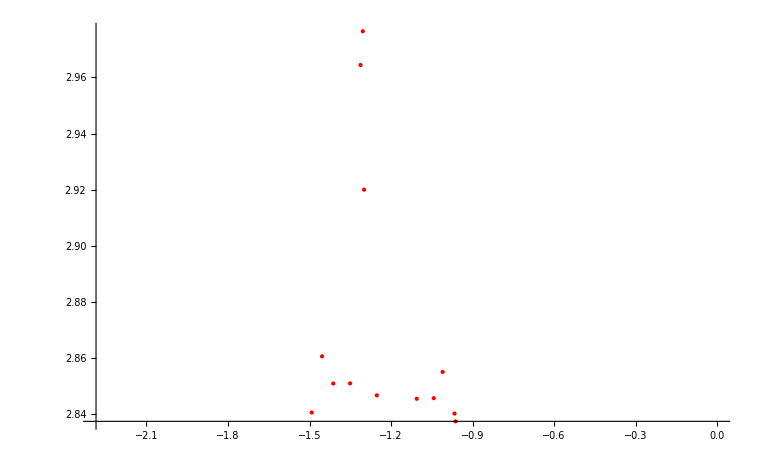

```mathematica
bondLenData = Import["/home/marco/fridbDemo/avgbondlen.json"] /. elementList;

lst=  "bnp" /. bondLenData[[1]];
lst = "38" /. lst;

lst = Delete[lst,3];
lst = Delete[lst,8];
bnp38BL = Table[x, {x,1,27}] /. lst;

bondLenVsBe38 = Partition[#,2] & @Riffle[#1, #2] & @@{smallBindingTable[[All,19]], bnp38BL}

 test=ListPlot[bondLenVsBe38[[11;;27]], PlotStyle->{Red,PointSize->Large}, PlotRange -> Automatic];

Show[test ]
```

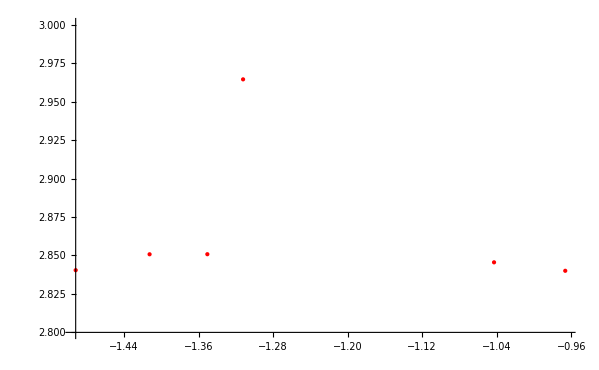
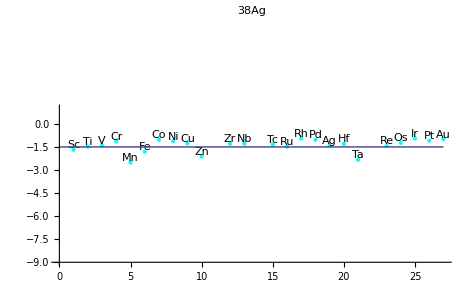

```mathematica
"38" /. "bnp" /. lst
```

ReplaceAll::reps: {"bnp"} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

38/.bnp

```mathematica
bnp/.%229
```

bnp

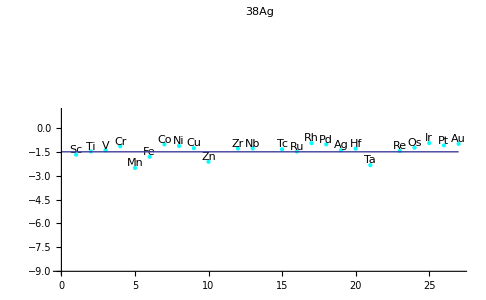
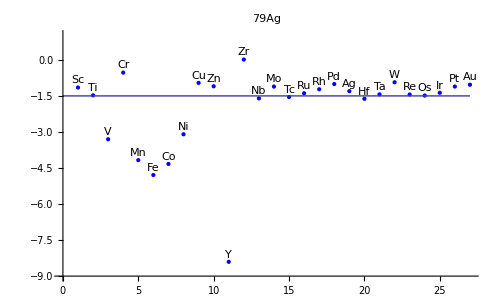
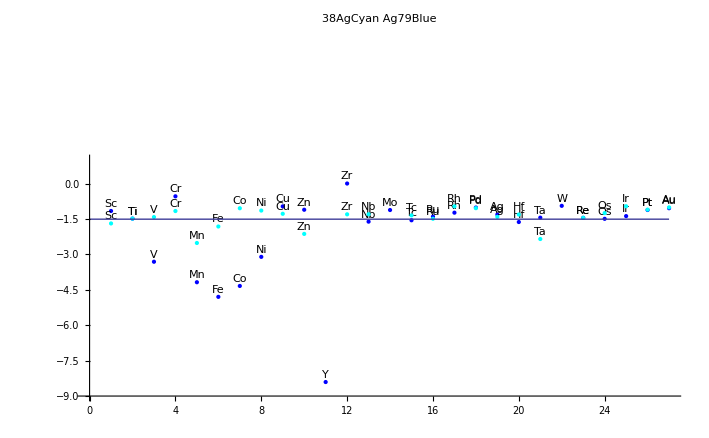
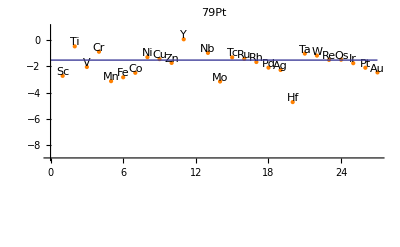
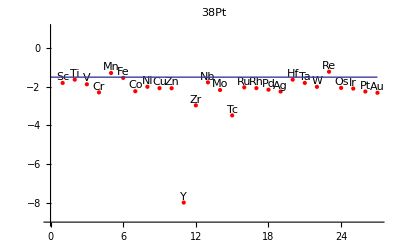
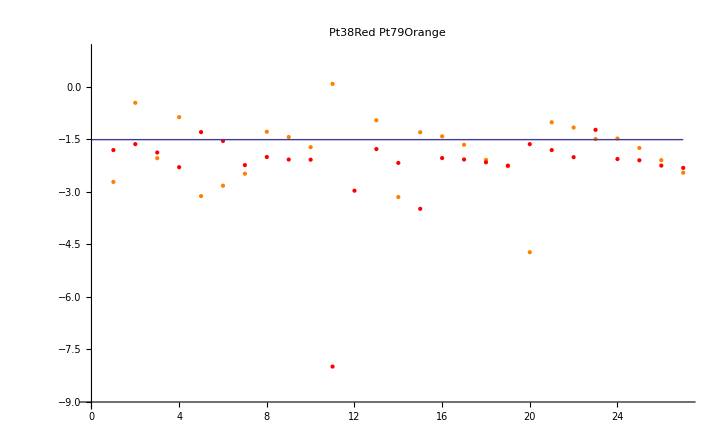
## Figures I want to keep: -Graphics--Graphics- -Graphics- -Graphics--Graphics- -Graphics-

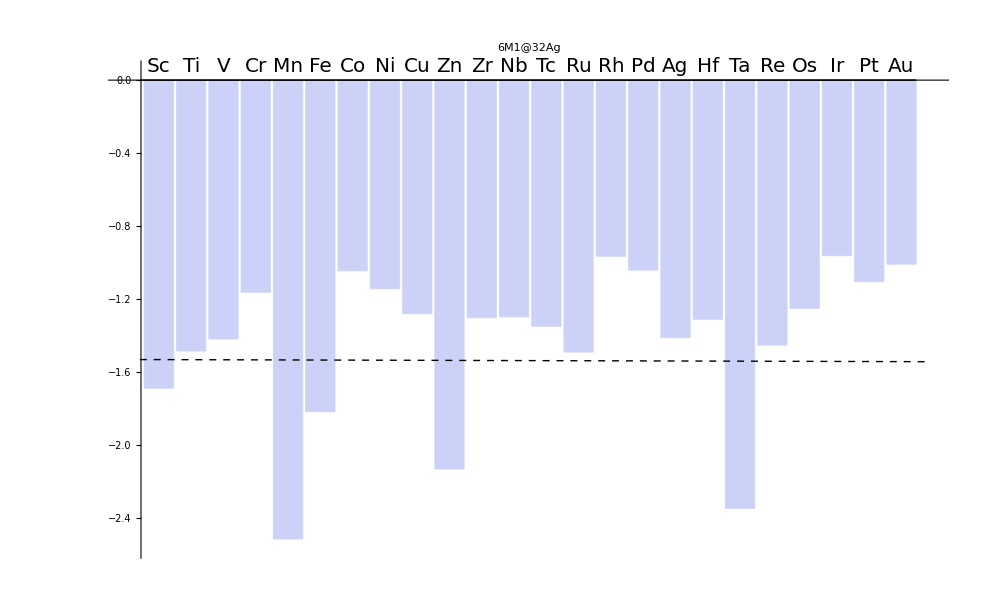

-Graphics-

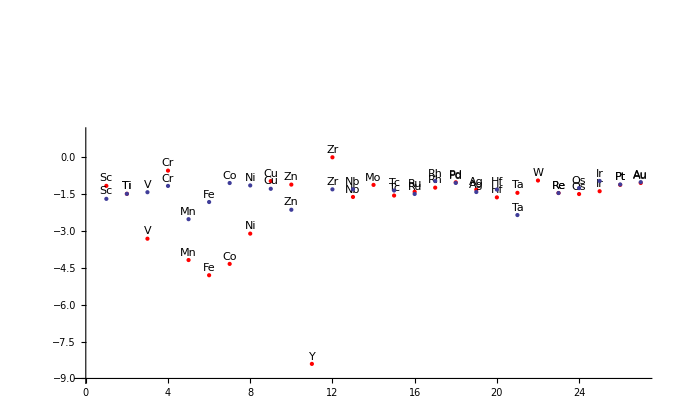

-Graphics-

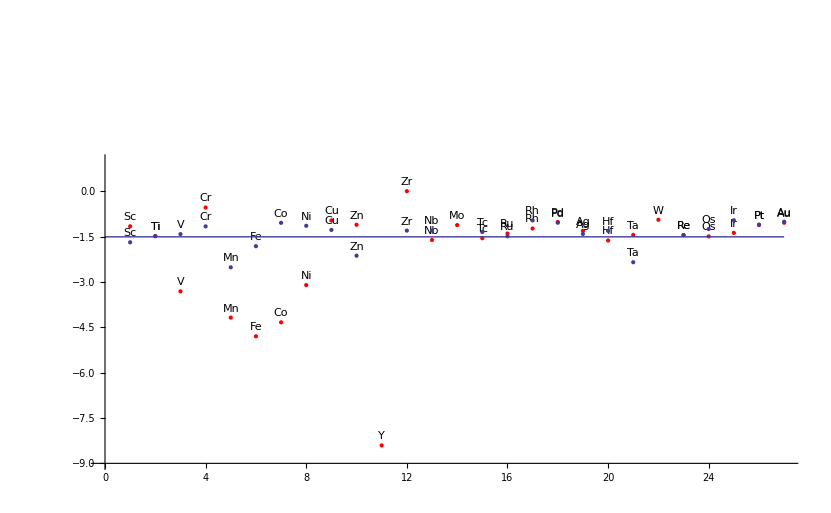

-Graphics-

```mathematica
Select[atoms32Binding,StringCases[#[[1]],"6/Ag/32/Ag/Binding Energy"]≠{}&]
rules=Cases[ atoms32Binding ,{__,"M1"->e1_,"M2"->e2_,__,"result"->val_,__}:>{e1,e2}->ToExpression@val,∞];
```

{6/Ag/32/Ag/Binding Energy→{a1→6,a2→32,M1→Ag,M2→Ag,metadata→6Ag@32Ag_npo: -87.926179 by mdh2736<br> 6Ag@32Ag_bnp: -82.091633 by mdh2736<br> O_sng:-8.843630 by mrl2225<br>,result→-1.41273086,result_type→Binding Energy,url→{s1→./database/6Ag@32Ag_npo/85fc9fe6fabc5f98f9e05c4294ca4411/CONTCAR,s2→./database/6Ag@32Ag_bnp/1247fe7ac3d788a30c43c5402d420608/CONTCAR},username→mdh2736}}

```mathematica
taget = -1.51
```

-1.51

```mathematica
subs = { r1 -> target - 0.2,r2 -> target + 0.2,  r3 -> (target -0.7, r3 -> (target +  0.7) + .3 } /. target -> -1.51
```

-Graphics-

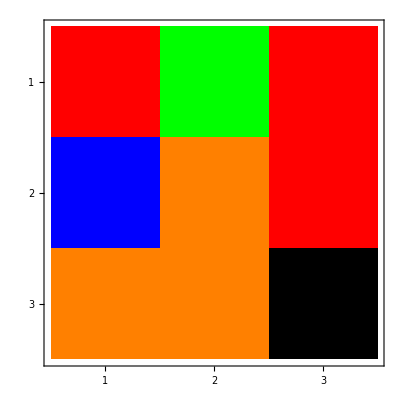

```mathematica
MatrixPlot[smallBindingTable[[All, 17;;21]], ColorRules->{x_/; r1 ≤x< r2 ->Orange /. subs,-r2≤x<r2->Red,x_/;-r3≤x<r3->Green,_->Black}]


MatrixPlot[{{1,2,1},{3,0,1},{0,0,-1}},ColorRules->{x_/;0≤x<1->Orange,x_/;1≤x<2->Red,x_/;2≤x<3->Green,x_/;3≤x<4->Blue,_->Black}]
```

```mathematica
-1.5 + .5
```

-1.

```mathematica
everything from -1to -2
```

-2+everything from-to

```mathematica
bigBindingTable[[All,26]]
```

{-2.71657,-0.458595,-2.03932,-0.868226,-3.12281,-2.82553,-2.48347,-1.28481,-1.4355,-1.72539,0.081853,-18.5892,-0.959019,-3.14932,-1.30003,-1.41603,-1.65717,-2.08796,-2.26764,-4.72443,-1.01418,-1.165,-1.49275,-1.47851,-1.7472,-2.09483,-2.45439}

```mathematica
-1.5 - (-1.1)
```

-0.4